## Basic patterns

```mathematica
Clear[f]
```

```mathematica
f[x]=1
```

1

```mathematica
f[y]=2
```

2

```mathematica
DownValues[f]
```

{HoldPattern[f[x]]:>1,HoldPattern[f[y]]:>2}

## Pattern matching

```mathematica
Clear[f]
```

```mathematica
f[x_]=x^2+2
```

2+x^2

```mathematica
f[3]
```

11

```mathematica
Clear[g]
```

```mathematica
g[x_Integer]:=x
```

```mathematica
g[x_Real]:=1/2 x
```

```mathematica
Head[3.0]
```

Real

```mathematica
?Real
```

```mathematica
Head[3]
```

Integer

```mathematica
?Integer
```

## Predicates in patterns

```mathematica
Clear[isOKForMe]
```

```mathematica
isOKForMe[x_]:=x<Pi|| x>3 Pi
```

```mathematica
isOKForMe[2]
```

True

```mathematica
Clear[h]
```

```mathematica
h[x_?isOKForMe]:=x
h[x_]:=Sin[x]
```

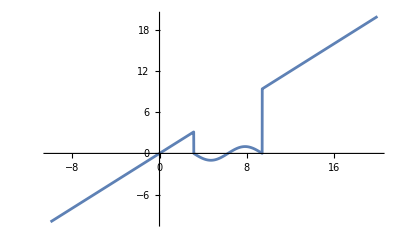

```mathematica
Plot[h[x],{x,-10,20}]
```

## SetDelayed and function caching

```mathematica
Clear[busyFun,veryLargeArg]
```

```mathematica
veryLargeArg=199090909090901909890909;
```

```mathematica
busyFun[x_]:=busyFun[x]=PrimeQ[x]
```

```mathematica
busyFun[veryLargeArg]//AbsoluteTiming
```

{0.000074,False}

```mathematica
busyFun[veryLargeArg]//AbsoluteTiming
```

{2.×10^-6,False}

```mathematica
busyFun[veryLargeArg]=.
```

```mathematica
busyFun[veryLargeArg]//AbsoluteTiming
```

{0.000064,False}

## Clearing the assignment

```mathematica
$PrePrint=MatrixForm
```

MatrixForm

```mathematica
{{1,2},{3,4}}
```

(1 | 2
3 | 4)

```mathematica
$PrePrint = .
```

```mathematica
{{1,2},{3,4}}
```

{{1,2},{3,4}}

```mathematica
$PrePrint=If[SquareMatrixQ[#],MatrixForm[#],#]&;
```

```mathematica
{{1,2,3},{4,5,6}}
```

{{1,2,3},{4,5,6}}

```mathematica
{{1,2},{3,4}}
```

(1 | 2
3 | 4)

## Pure functions

```mathematica
fun1=#+#^2+3 #^3&
```

#1+#1^2+3 #1^3&

```mathematica
Map[fun1,Range[10]]
```

{5,30,93,212,405,690,1085,1608,2277,3110}

## Problem 1 from ProjectEuler

If we list all the natural numbers below 10 that are multiples of 3 or 5, we get 3, 5, 6 and 9. The sum of these multiples is 23. Find the sum of all the multiples of 3 or 5 below 1000.

```mathematica
divBy3or5=If[Mod[#,3]==0 || Mod[#,5]==0 ,#,0]&;
```

```mathematica
list1=Map[divBy3or5,Range[999]];
```

```mathematica
Total[list1]
```

233168

```mathematica
Plus@@list1
```

233168

```mathematica
divBy3or5=Mod[#,3]==0 || Mod[#,5]==0 &
```

Mod[#1,3]==0||Mod[#1,5]==0&

```mathematica
Select[Range[999],divBy3or5]//Total
```

233168

## Clearing

```mathematica
Set[x,0]
```

0

```mathematica
{OwnValues[x],OwnValues[y]}
```

{{HoldPattern[x]:>0},{}}

```mathematica
x
```

0

```mathematica
SetDelayed[y,Random[]]
```

## UpValues

```mathematica
?UpValues
```

```mathematica
g/:f[g[x_]]:=x+1
```

```mathematica
UpValues[g]
```

{HoldPattern[f[g[x_]]]:>x+1}

```mathematica
f[g[1]]
```

3